```mathematica
coords={x,y,z};
vel={u[x,y,z],v[x,y,z],w[x,y,z]};
gvel=Grad[vel,coords];
dvel=Div[vel,coords];

tau = ζ dvel IdentityMatrix[3] + η (gvel + Transpose[gvel] - 2/3 dvel IdentityMatrix[3])
```

{{ζ (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])+η (2 u^(1,0,0)[x,y,z]-2/3 (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])),η (u^(0,1,0)[x,y,z]+v^(1,0,0)[x,y,z]),η (u^(0,0,1)[x,y,z]+w^(1,0,0)[x,y,z])},{η (u^(0,1,0)[x,y,z]+v^(1,0,0)[x,y,z]),ζ (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])+η (2 v^(0,1,0)[x,y,z]-2/3 (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])),η (v^(0,0,1)[x,y,z]+w^(0,1,0)[x,y,z])},{η (u^(0,0,1)[x,y,z]+w^(1,0,0)[x,y,z]),η (v^(0,0,1)[x,y,z]+w^(0,1,0)[x,y,z]),ζ (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])+η (2 w^(0,0,1)[x,y,z]-2/3 (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z]))}}

```mathematica
tau[[3]]
```

{η (u^(0,0,1)[x,y,z]+w^(1,0,0)[x,y,z]),η (v^(0,0,1)[x,y,z]+w^(0,1,0)[x,y,z]),ζ (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])+η (2 w^(0,0,1)[x,y,z]-2/3 (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z]))}

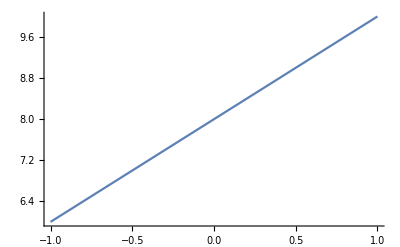

```mathematica
cellT=10;
bcT=8;
tList={{-1,-cellT+2bcT},{1,cellT}};

ListPlot[tList,Joined->True]
```

```mathematica
Tr[tau]
```

0.333333 (3 ζ (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])+η (2 w^(0,0,1)[x,y,z]-2/3 (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z]))+η (2 v^(0,1,0)[x,y,z]-2/3 (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z]))+η (2 u^(1,0,0)[x,y,z]-2/3 (w^(0,0,1)[x,y,z]+v^(0,1,0)[x,y,z]+u^(1,0,0)[x,y,z])))